# Two point function

```mathematica
M = 1000; (* Discretization -> number of lattice sites on the chain ; lattice integrals have 1/M corrections *)
η = 0.0000001;
J = 10;
dd2[n_,g_ ,T_] :=Chop[ 1/M Sum[Chop[Exp[- I n ϕ] √((1 - g Exp[I ϕ])/(1- g Exp[-I ϕ]))Tanh[J/T((1 - g Exp[I ϕ])(1- g Exp[-I ϕ]))^(1/2)]], {ϕ,0 + 2 Pi/M,2Pi(1-1/M), 2 Pi/M}]]
dd[n_,g_,T_] := Chop[1/(2 Pi)NIntegrate[Exp[- I n ϕ] √((1 - g Exp[I ϕ])/(1- g Exp[-I ϕ]))Tanh[J/T((1 - g Exp[I ϕ])(1- g Exp[-I ϕ]))^(1/2)]/. ϕ -> ϕ - I η,{ϕ,0,2 Pi},AccuracyGoal->6,WorkingPrecision->8,MaxRecursion->20] ]
(*     <<Subscript[A, 0](t)Subscript[A, n](0)(>>)_β     *)
eps[p_,g_] := 2 J √(1 + g^2 - 2 g Cos[p]); 
ffd[ϵ_, T_] := 1/(1 + Exp[ϵ/T]);
ACorr0t[n_,g_,T_,t_] := Chop[1/(2 Pi)NIntegrate[Chop[Exp[I n p] (Exp[I eps[p,g]t] ffd[eps[p,g],T] + Exp[-I eps[p,g]t] ffd[-eps[p,g],T])] /. p -> p + I η, {p,0,2 Pi}, AccuracyGoal->6]];
ACorr0t2[n_,g_,T_,t_] := Chop[1/M Sum[Chop[Exp[I n p] (Exp[I eps[p,g]t] ffd[eps[p,g],T] + Exp[-I eps[p,g]t] ffd[-eps[p,g],T])], {p,0,2 Pi, 2 Pi/M}]];

nmax = 25; (* Maximum number of sites for which the correlator is obtained *)
tmax = 25; (*Maximum time at which the correlator is obtained *)
g = 1;
T = 1; 
tim = AbsoluteTime[];
corr = Table[0 , {i,nmax}, {j,tmax}];
(*dd2list = <|Table[i -> Chop[N[dd2[i,g,T]]] , {i,-nmax,nmax}]|> ;*)
ddlist = <|Table[i -> Chop[N[dd[i,g,T]]] , {i,-nmax,nmax}]|> ;
For[ n = 1 , n  ≤ nmax, n++ ,  
ttmat = Table[ddlist[i-j],{i,n},{j,n}] ; ; 
insrow = Table[ddlist[i],{i,n}];

For[ t = 0, t < tmax, t++, 
temp = PrintTemporary["Calculating for n = ", n, " t = ", t, ". Previous iteration done in ", AbsoluteTime[]-tim, " seconds."];
tim = AbsoluteTime[];
init = Chop[N[ACorr0t[0,g,T,t] * Det[ttmat]]]; 

For[i=1,i≤n,i++, 
swapmat = ttmat ;
swapmat[[All,i]] = insrow;
init = init - (Chop[N[ACorr0t[i,g,T,t]* Det[swapmat]]]) ; 
];
corr[[n,t+1]] = N[Chop[init]];
NotebookDelete[temp];
] 
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.144322}. NIntegrate obtained 0.211836-0.0023062 ⅈ and 2.64297×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {6.1388630836360589260181086501688696444034576416015625}. NIntegrate obtained -0.211827+0.00306275 ⅈ and 2.64774×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {6.1388630836360589260181086501688696444034576416015625}. NIntegrate obtained 0.138656+0.150541 ⅈ and 5.39072×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Export["~/Documents/CorrXmax25Tmax25_g1_T1.dat",corr]
```

~/Documents/CorrXmax25Tmax25_g1_T1.dat

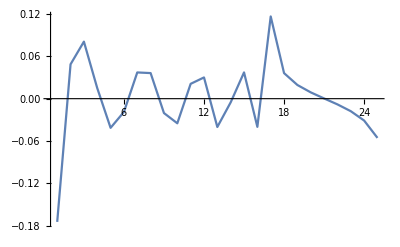

```mathematica
ListLinePlot[Im[Fourier[corr[[10 , All]]]], PlotRange->Full]
```

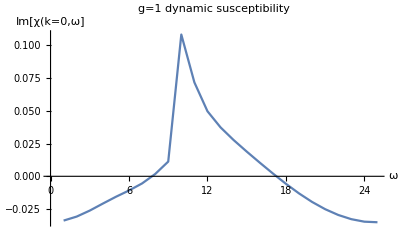

```mathematica
chi = Fourier[corr] ;
ListLinePlot[Im[chi[[1,All]]], AxesLabel-> {"ω","Im[χ(k=0,ω]" }, PlotLabel -> "g=1 dynamic susceptibility"]
```

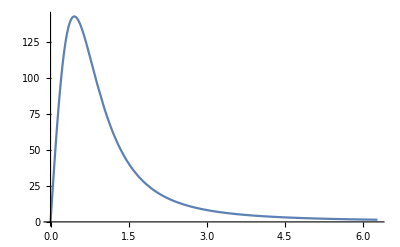

```mathematica
sachchikw[ω_,k_,T_] := 1/T^(7/4)  (Gamma[1/16 - I (ω + k)/(4Pi T)] Gamma[1/16 - I (ω - k)/(4Pi T)])/(Gamma[15/16 - I (ω + k)/(4Pi T)] Gamma[15/16 - I (ω - k)/(4Pi T)]) 
Plot[Im[sachchikw[ω,0,1]],{ω,0,2Pi}, PlotRange->Full]
```

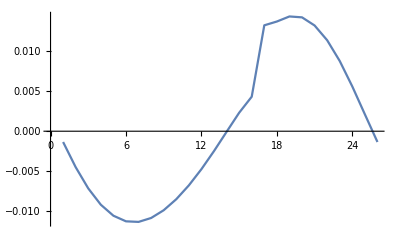

```mathematica
chik0hand = Table[1/nmax 1/tmax Sum[Sum[corr[[x,t]]Exp[-I ω t],{x,1,nmax}],{t,1,tmax}], {ω,0,2Pi,2 Pi/tmax}];
ListLinePlot[Im[chik0hand]]
```